# Verifications of integrals evaluation

## For comparison with integralARB package

## Overview of test cases

=== SUMMARY: All Test Functions ===

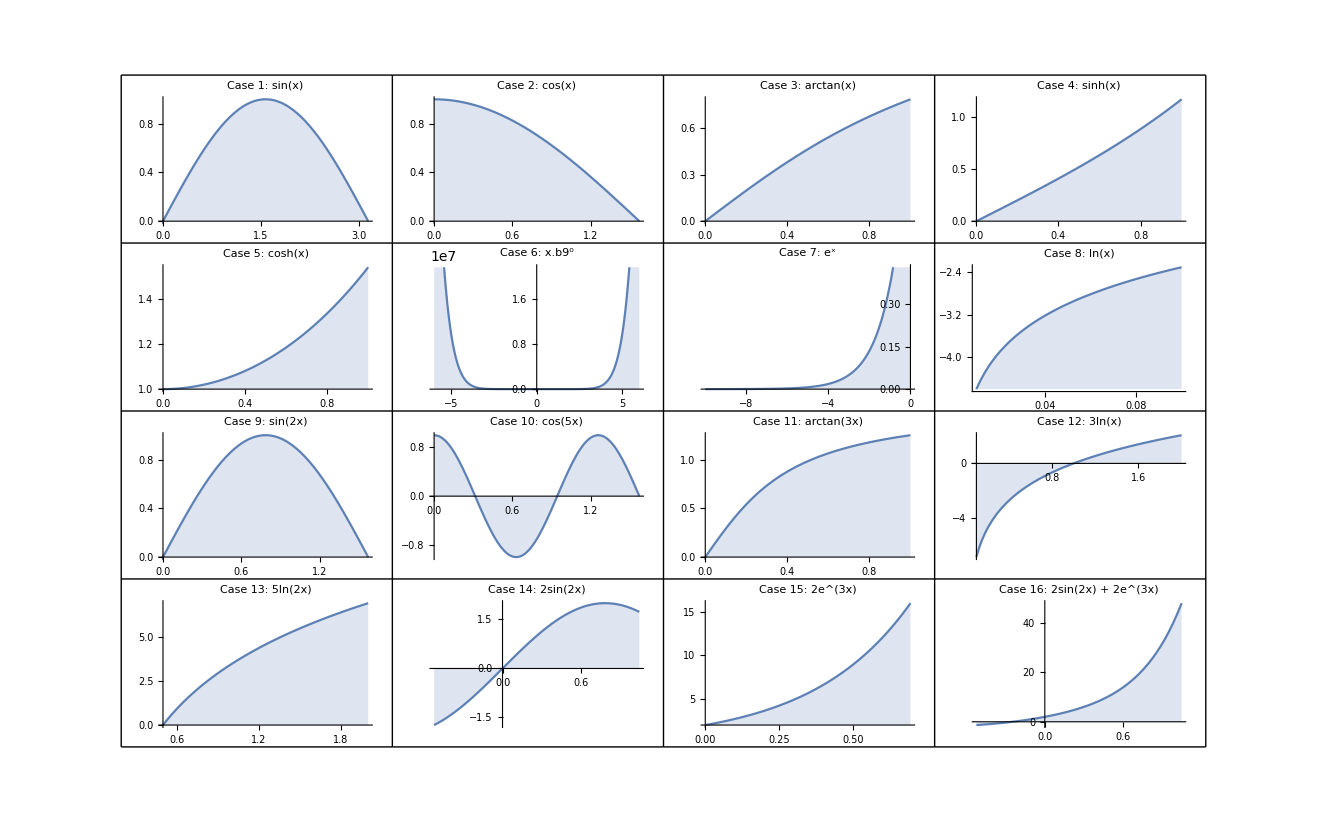

```mathematica
(* Create a summary plot showing all functions *)
Print["=== SUMMARY: All Test Functions ==="];
GraphicsGrid[{
  {Plot[Sin[x], {x, 0, Pi}, Filling -> Axis, PlotLabel -> "Case 1: sin(x)", ImageSize -> 200],
   Plot[Cos[x], {x, 0, Pi/2}, Filling -> Axis, PlotLabel -> "Case 2: cos(x)", ImageSize -> 200],
   Plot[ArcTan[x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 3: arctan(x)", ImageSize -> 200],
   Plot[Sinh[x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 4: sinh(x)", ImageSize -> 200]},
  {Plot[Cosh[x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 5: cosh(x)", ImageSize -> 200],
   Plot[x^10, {x, -6, 6}, Filling -> Axis, PlotLabel -> "Case 6: x.b9⁰", ImageSize -> 200],
   Plot[Exp[x], {x, -10, 0}, Filling -> Axis, PlotLabel -> "Case 7: eˣ", ImageSize -> 200],
   Plot[Log[x], {x, 0.01, 0.1}, Filling -> Axis, PlotLabel -> "Case 8: ln(x)", ImageSize -> 200]},
  {Plot[Sin[2*x], {x, 0, Pi/2}, Filling -> Axis, PlotLabel -> "Case 9: sin(2x)", ImageSize -> 200],
   Plot[Cos[5*x], {x, 0, Pi/2}, Filling -> Axis, PlotLabel -> "Case 10: cos(5x)", ImageSize -> 200],
   Plot[ArcTan[3*x], {x, 0, 1}, Filling -> Axis, PlotLabel -> "Case 11: arctan(3x)", ImageSize -> 200],
   Plot[3*Log[x], {x, 0.1, 2}, Filling -> Axis, PlotLabel -> "Case 12: 3ln(x)", ImageSize -> 200]},
  {Plot[5*Log[2*x], {x, 0.5, 2}, Filling -> Axis, PlotLabel -> "Case 13: 5ln(2x)", ImageSize -> 200],
   Plot[2*Sin[2*x], {x, -Pi/6, Pi/3}, Filling -> Axis, PlotLabel -> "Case 14: 2sin(2x)", ImageSize -> 200],
   Plot[2*Exp[3*x], {x, 0, Log[2]}, Filling -> Axis, PlotLabel -> "Case 15: 2e^(3x)", ImageSize -> 200],
   Plot[2*Sin[2*x] + 2*Exp[3*x], {x, -Pi/6, Pi/3}, Filling -> Axis, PlotLabel -> "Case 16: 2sin(2x) + 2e^(3x)", ImageSize -> 200]}
}, Frame -> All]
```

## Testing on September 10, 2025

We will test the precision of integralARB R package with 16 different integrals. The answer will range from integers to rational and irrational numbers to best evaluate the precision attainable by the package. With this Mathematica notebook, we will try to solve each integral symbolically before getting the decimal representation in high precision to minimize errors in computation.

Split the code by case. Put the overview with all the graph to the beginning.

=== Case 1: ∫ sin(x) dx ===

Symbolic result: 2

High precision value: 2.

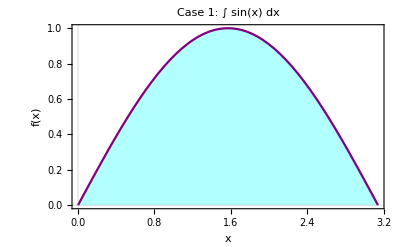

Exact value: 2.

=== Case 2: ∫ cos(x) dx ===

Symbolic result: 1

High precision value: 1.

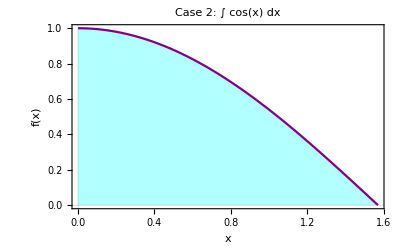

Exact value: 1.

=== Case 3: ∫ arctan(x) dx ===

Symbolic result: 1/4 (π-Log[4])

High precision value: 0.43882457311747565490704478509078743701154228266365

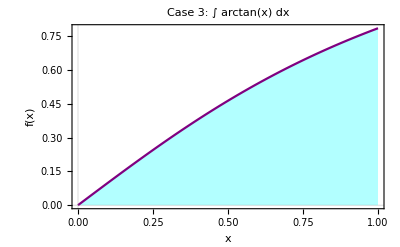

Exact value: 0.43882457311747565490704478509078743701154228266365

=== Case 4: ∫ sinh(x) dx ===

Symbolic result: -1+Cosh[1]

High precision value: 0.54308063481524377847790562075706168260152911236586

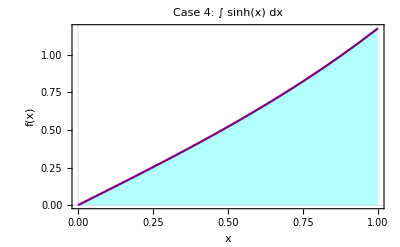

Exact value: 0.54308063481524377847790562075706168260152911236586

=== Case 5: ∫ cosh(x) dx ===

Symbolic result: Sinh[1]

High precision value: 1.1752011936438014568823818505956008151557179813341

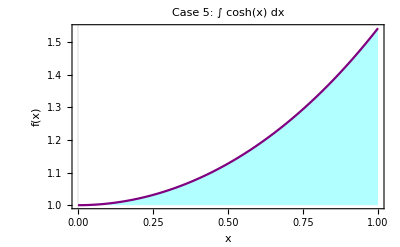

Exact value: 1.1752011936438014568823818505956008151557179813341

=== Case 6: ∫ x.b9⁰ dx ===

Symbolic result: 725594112/11

High precision value: 6.5963101090909090909090909090909090909090909090909×10^7

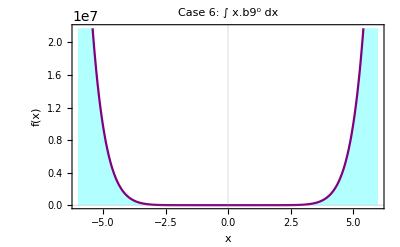

Exact value: 6.5963101090909090909090909090909090909090909090909×10^7

=== Case 7: ∫ eˣ dx ===

Symbolic result: 1-1/ⅇ^10

High precision value: 0.99995460007023751514846440848443944938976208191113

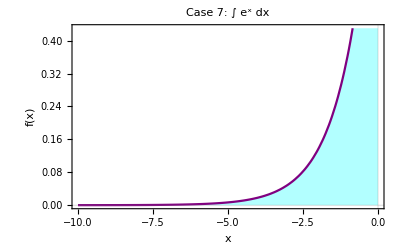

Exact value: 0.99995460007023751514846440848443944938976208191113

=== Case 8: ∫ ln(x) dx ===

Symbolic result: 1/100 (-9-8 Log[10])

High precision value: -0.2742068074395236547214393163747491366080881190903

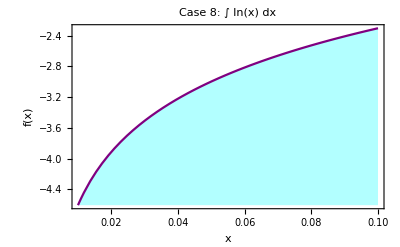

Exact value: -0.2742068074395236547214393163747491366080881190903

=== Case 9: ∫ sin(2x) dx ===

Symbolic result: 1

High precision value: 1.

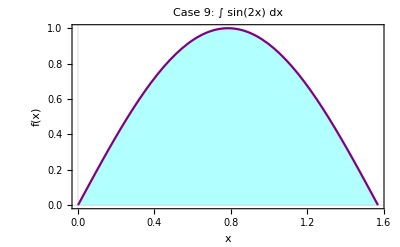

Exact value: 1.

=== Case 10: ∫ cos(5x) dx ===

Symbolic result: 1/5

High precision value: 0.2

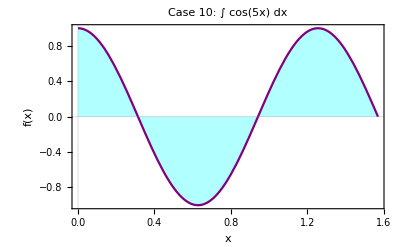

Exact value: 0.2

=== Case 11: ∫ arctan(3x) dx ===

Symbolic result: ArcTan[3]-Log[10]/6

High precision value: 0.86528159023258014516025183483369608847764582269177

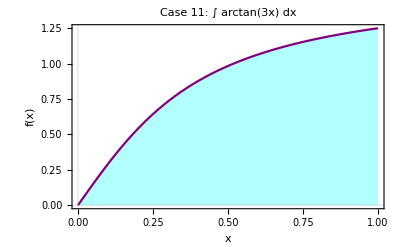

Exact value: 0.86528159023258014516025183483369608847764582269177

=== Case 12: ∫ 3ln(x) dx ===

Symbolic result: 3/10 (-19+10 Log[4]+Log[10])

High precision value: -0.85034138874211443829120983484563132926666874724984

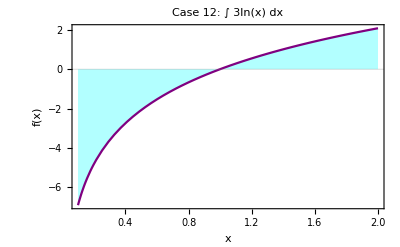

Exact value: -0.85034138874211443829120983484563132926666874724984

=== Case 13: ∫ 5ln(2x) dx ===

Symbolic result: 5 (-3/2+Log[16])

High precision value: 6.3629436111989061883446424291635313615100026872051

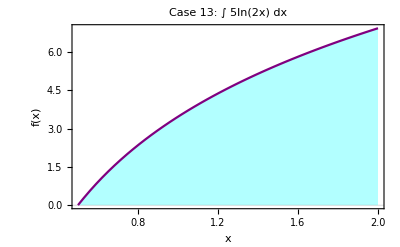

Exact value: 6.3629436111989061883446424291635313615100026872051

=== Case 14: ∫ 2sin(2x) dx ===

Symbolic result: 1

High precision value: 1.

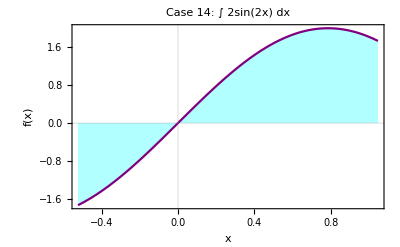

Exact value: 1.

=== Case 15: ∫ 2e^(3x) dx ===

Symbolic result: 14/3

High precision value: 4.6666666666666666666666666666666666666666666666667

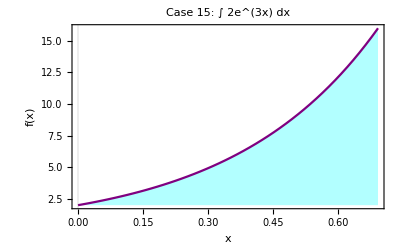

Exact value: 4.6666666666666666666666666666666666666666666666667

=== Case 16: ∫[2sin(2x) + 2e^(3x)] dx ===

Symbolic result: 1-(2 ⅇ^(-π/2))/3+(2 ⅇ^π)/3

High precision value: 16.288542037619004731454753832075712406821485600646

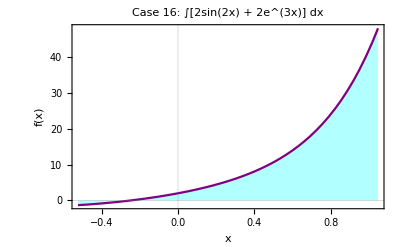

Exact value: 16.288542037619004731454753832075712406821485600646

Case 8 - Exact bounds: 1/100 (-9-8 Log[10])

Case 12 - Exact bounds: 3/10 (-19+10 Log[4]+Log[10])

Case 13 - Exact bounds: 5 (-3/2+Log[16])

Verifying against table values:

Case 8 - Table vs Computed: -0.27420680743952365472 vs exact8Simplified

Case 12 - Table vs Computed: -0.85034138874211443829 vs -0.85034138874211443829

Case 13 - Table vs Computed: 6.3629436111989061883 vs 6.3629436111989061883

```mathematica
(* Set high precision for calculations *)
$MaxExtraPrecision = 200;
precision = 50;

(* Function to compute integral symbolically first, then numerically if needed *)
computeIntegral[integrand_, var_, limits_, caseNum_, description_] := Module[
  {symbolic, exact, numerical, plot},
  
  Print["=== Case ", caseNum, ": ", description, " ==="];
  
  (* Try symbolic integration first *)
  symbolic = Quiet[Integrate[integrand, {var, limits[[1]], limits[[2]]}]];
  
  If[FreeQ[symbolic, Integrate],
    (* Symbolic integration succeeded *)
    exact = N[symbolic, precision];
    Print["Symbolic result: ", symbolic];
    Print["High precision value: ", exact],
    (* Symbolic failed, use high-precision numerical *)
    exact = NIntegrate[integrand, {var, limits[[1]], limits[[2]]}, 
           WorkingPrecision -> precision];
    Print["Symbolic integration failed, using numerical: ", exact]
  ];
  
  (* Create plot *)
  plot = Plot[integrand, {var, limits[[1]], limits[[2]]}, 
    PlotStyle -> Purple, 
    Filling -> Axis, 
    FillingStyle -> Opacity[0.3, Cyan],
    PlotLabel -> "Case " <> ToString[caseNum] <> ": " <> description,
    AxesLabel -> {ToString[var], "f(" <> ToString[var] <> ")"},
    PlotTheme -> "Scientific",
    ImageSize -> 400];
  
  Print[plot];
  Print["Exact value: ", exact];
  Print[];
  
  Return[exact]
];

(* Case 1: Simple integral - sin(x) *)
exact1 = computeIntegral[Sin[x], x, {0, Pi}, 1, "∫ sin(x) dx"];

(* Case 2: Simple integral - cos(x) *)
exact2 = computeIntegral[Cos[x], x, {0, Pi/2}, 2, "∫ cos(x) dx"];

(* Case 3: ArcTan integral *)
exact3 = computeIntegral[ArcTan[x], x, {0, 1}, 3, "∫ arctan(x) dx"];

(* Case 4: Sinh integral *)
exact4 = computeIntegral[Sinh[x], x, {0, 1}, 4, "∫ sinh(x) dx"];

(* Case 5: Cosh integral *)
exact5 = computeIntegral[Cosh[x], x, {0, 1}, 5, "∫ cosh(x) dx"];

(* Case 6: Polynomial integral *)
exact6 = computeIntegral[x^10, x, {-6, 6}, 6, "∫ x.b9⁰ dx"];

(* Case 7: Exponential integral *)
exact7 = computeIntegral[Exp[x], x, {-10, 0}, 7, "∫ eˣ dx"];

(* Case 8: Log integral *)
exact8 = computeIntegral[Log[x], x, {1/100, 1/10}, 8, "∫ ln(x) dx"];

(* Case 9: Chain rule - sin(2x) *)
exact9 = computeIntegral[Sin[2*x], x, {0, Pi/2}, 9, "∫ sin(2x) dx"];

(* Case 10: Chain rule - cos(5x) *)
exact10 = computeIntegral[Cos[5*x], x, {0, Pi/2}, 10, "∫ cos(5x) dx"];

(* Case 11: Chain rule - arctan(3x) *)
exact11 = computeIntegral[ArcTan[3*x], x, {0, 1}, 11, "∫ arctan(3x) dx"];

(* Case 12: Combined - 3*ln(x) *)
exact12 = computeIntegral[3*Log[x], x, {1/10, 2}, 12, "∫ 3ln(x) dx"];

(* Case 13: Combined - 5*ln(2x) *)
exact13 = computeIntegral[5*Log[2*x], x, {1/2, 2}, 13, "∫ 5ln(2x) dx"];

(* Case 14: Combined - 2*sin(2x) *)
exact14 = computeIntegral[2*Sin[2*x], x, {-Pi/6, Pi/3}, 14, "∫ 2sin(2x) dx"];

(* Case 15: Combined - 2*exp(3x) *)
exact15 = computeIntegral[2*Exp[3*x], x, {0, Log[2]}, 15, "∫ 2e^(3x) dx"];

(* Case 16: Combined - sum *)
exact16 = computeIntegral[2*Sin[2*x] + 2*Exp[3*x], x, {-Pi/6, Pi/3}, 16, 
  "∫[2sin(2x) + 2e^(3x)] dx"];
```

## Symbolic and 50-digit precision summary

```mathematica
(* Summary table of all exact values *)
Print["=== SUMMARY OF EXACT VALUES (50-digit precision) ==="];
Print["Case  1: ", exact1];
Print["Case  2: ", exact2];
Print["Case  3: ", exact3];
Print["Case  4: ", exact4];
Print["Case  5: ", exact5];
Print["Case  6: ", exact6];
Print["Case  7: ", exact7];
Print["Case  8: ", exact8];
Print["Case  9: ", exact9];
Print["Case 10: ", exact10];
Print["Case 11: ", exact11];
Print["Case 12: ", exact12];
Print["Case 13: ", exact13];
Print["Case 14: ", exact14];
Print["Case 15: ", exact15];
Print["Case 16: ", exact16];

(* Export exact symbolic forms *)
Print["=== EXACT SYMBOLIC FORMS ==="];
Print["Case  1: ", Integrate[Sin[x], {x, 0, Pi}]];
Print["Case  2: ", Integrate[Cos[x], {x, 0, Pi/2}]];
Print["Case  3: ", Integrate[ArcTan[x], {x, 0, 1}]];
Print["Case  4: ", Integrate[Sinh[x], {x, 0, 1}]];
Print["Case  5: ", Integrate[Cosh[x], {x, 0, 1}]];
Print["Case  6: ", Integrate[x^10, {x, -6, 6}]];
Print["Case  7: ", Integrate[Exp[x], {x, -10, 0}]];
Print["Case  8: ", Integrate[Log[x], {x, 0.01, 0.1}]];
Print["Case  9: ", Integrate[Sin[2*x], {x, 0, Pi/2}]];
Print["Case 10: ", Integrate[Cos[5*x], {x, 0, Pi/2}]];
Print["Case 11: ", Integrate[ArcTan[3*x], {x, 0, 1}]];
Print["Case 12: ", Integrate[3*Log[x], {x, 0.1, 2}]];
Print["Case 13: ", Integrate[5*Log[2*x], {x, 0.5, 3}]];
Print["Case 14: ", Integrate[2*Sin[2*x], {x, Pi/6, Pi/3}]];
Print["Case 15: ", Integrate[2*Exp[3*x], {x, 0, Log[2]}]];
Print["Case 16: ", Integrate[2*Sin[2*x] + 2*Exp[3*x], {x, Pi/6, Pi/3}]];
```

=== SUMMARY OF EXACT VALUES (50-digit precision) ===

Case  1: 2.

Case  2: 1.

Case  3: 0.43882457311747565490704478509078743701154228266365

Case  4: 0.54308063481524377847790562075706168260152911236586

Case  5: 1.1752011936438014568823818505956008151557179813341

Case  6: 6.5963101090909090909090909090909090909090909090909×10^7

Case  7: 0.99995460007023751514846440848443944938976208191113

Case  8: -0.2742068074395236547214393163747491366080881190903

Case  9: 1.

Case 10: 0.2

Case 11: 0.86528159023258014516025183483369608847764582269177

Case 12: -0.85034138874211443829120983484563132926666874724984

Case 13: 6.3629436111989061883446424291635313615100026872051

Case 14: 1.

Case 15: 4.6666666666666666666666666666666666666666666666667

Case 16: 16.288542037619004731454753832075712406821485600646

=== EXACT SYMBOLIC FORMS ===

Case  1: 2

Case  2: 1

Case  3: 1/4 (π-Log[4])

Case  4: -1+Cosh[1]

Case  5: Sinh[1]

Case  6: 725594112/11

Case  7: 1-1/ⅇ^10

Case  8: -0.274207

Case  9: 1

Case 10: 1/5

Case 11: ArcTan[3]-Log[10]/6

Case 12: -0.850341

Case 13: 14.3764

Case 14: 1

Case 15: 14/3

Case 16: 1/3 (3-2 ⅇ^(π/2)+2 ⅇ^π)